## Miscellaneous functions

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["TenGSHui`","~/ownCloud/Shared/TenGSHui.m"];TenGSHui`FastMode=True;
TOneSide:=If[!SameQ[#[[2]],0],(Head[#][TMinus@@#,0]),#]&
OneSide:=If[!SameQ[#[[2]],0],(Head[#][Subtract@@#,0]),#]&
ClearAll[GetDiffOrder]
GetDiffOrder[expr_,fields_List]:=Module[{order},
Max[0,Max[Cases[expr,Derivative[order_][head_?(MemberQ[fields,#]&)]->order,∞,Heads->True]]]]
SplitColumnwise[mat_,dim_]:=Module[{first=Accumulate[{1}~Join~Most@dim],last=Accumulate@dim},MapThread[mat[[All,#1;;#2]]&,{first,last}]]
AllCoefficientArrays[eq_,var__]:=Module[{bigmat,coef=CoefficientArrays[eq,Join[var]]},
If[SameQ[Length[coef],1],
coef={First@coef,SparseArray[{},{Length[First@coef],Length[Join@var]}]};
];
bigmat=SparseArray@Simplify@Last@coef;
{Most@coef,SplitColumnwise[bigmat,Length/@{var}]}]
```

Loading TenGSHui...

Done. Please execute DisplayPalette if you need the palette.

## Sprouts

```mathematica
ClearAll["Sprouts`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["SproutsFun`","./SproutsFun.m"]
```

```mathematica
ClearAll[PartitionDomain]
PartitionDomain[domain_List]:=
Block[{},
(* arrange layers and check if the first one contains the origin *)
Block[{partition=Partition[Sort@Rest[domain],2,1]},
Sprouts`nlayers=Length[partition];
Table[Sprouts`layer[i]=partition⟦i⟧,{i,1,Sprouts`nlayers}];
]
If[SameQ[N@First[Sprouts`layer[1]],0.],
Sprouts`zeroInDomain=True;,
Sprouts`zeroInDomain=False;
];
Echo[Table[Sprouts`layer[i],{i,1,Sprouts`nlayers}],"partition of the spatial domain :"];
(* rescale physical subdomains to u∈[0,1] or uϵ[-1,1] *)
Block[{cdom},
If[Sprouts`zeroInDomain,
Sprouts`rfu[1][u_]=Rescale[u,{0,1},Sprouts`layer[1]];
Sprouts`ufr[1][r_]=Rescale[r,Sprouts`layer[1],{0,1}];,
Sprouts`rfu[1][u_]=Rescale[u,{-1,1},Sprouts`layer[1]];
Sprouts`ufr[1][r_]=Rescale[r,Sprouts`layer[1],{-1,1}];
];
Sprouts`drdu[1]=Sprouts`rfu[1]'[u];
Table[
Sprouts`rfu[k][u_]=Rescale[u,{-1,1},Sprouts`layer[k]];
	Sprouts`ufr[k][r_]=Rescale[r,Sprouts`layer[k],{-1,1}];
	Sprouts`drdu[k]=Sprouts`rfu[k]'[u]
,{k,2,Sprouts`nlayers}]
];
]
```

```mathematica
ClearAll[AnalyseProblem]
AnalyseProblem[λsymbol_Symbol,{ℓmin_Integer,ℓmax_Integer,𝓂min_Integer,𝓂max_Integer}]:=AnalyseProblem[λsymbol,Flatten[Table[{ℓ,𝓂},{ℓ,ℓmin,ℓmax},{𝓂,Max[𝓂min,-ℓ],Min[𝓂max,ℓ]}],1]];
AnalyseProblem[λsymbol_Symbol,rangeℓ𝓂_]:=
Module[{λ=λsymbol,pos,tab},
(* get the maximum power in the eigenvalue *)
Sprouts`λmax=Max@(Exponent[#,λ]&/@Flatten[{Sprouts`eq,Sprouts`rbc}]);
If[!SameQ[Sprouts`λmax,0],
Sprouts`evp=True;Echo[Sprouts`λmax,"eigenvalue problem of order : "];,
Sprouts`evp=False;Echo["","linear problem of the type Ax=b"]
];

pos=Table[(* loop layers *)
Flatten@Position[
Flatten@Table[(* loop scalars *)
Flatten@Table[(* loop SH *)
Sprouts`scalars⟦k,i⟧[][Sequence@@ind][r]
,{ind,rangeℓ𝓂}]
,{i,1,Length@Sprouts`scalars⟦k⟧}]
,f_[ℓ_,𝓂_][r_],{1}]
,{k,1,Sprouts`nlayers}];

tab=Table[Table[Table[Derivative[i][Sprouts`scalars⟦k,j⟧[][Sequence@@ind]][r],{ind,rangeℓ𝓂}],{j,1,Length@Sprouts`scalars⟦k⟧}]//Flatten,{k,1,Sprouts`nlayers}];

Sprouts`listvar=Table[Table[Part[tab⟦k⟧,pos⟦k⟧],{i,0,Sprouts`ndiff}],{k,1,Sprouts`nlayers}];
Sprouts`layout=Table[(Head/@Part[Sprouts`listvar⟦k⟧,1]),{k,1,Sprouts`nlayers}];
Echo[Sprouts`layout,"layout of the solution : "];

If[Sprouts`zeroInDomain,
Sprouts`nColTotal=(Total[(Length/@Sprouts`layout)*Sprouts`n]-(First@Sprouts`n)/2 Length[First@Sprouts`layout]),Sprouts`nColTotal=(Length/@Sprouts`layout)*Sprouts`n];
WriteString["stdout","Size of the final matrices = ",ToString[Sprouts`nColTotal],"x",ToString[Sprouts`nColTotal],"\n"];

If[Sprouts`zeroInDomain,
Echo["","regularity conditions will be enforced at r=0 based on indices of spherical harmonics"];
Which[
	SameQ[Sprouts`coordinates,"Spherical"],
	(* indices of even and odd functions based on their ℓ *)
Sprouts`eid=
Table[(* loop layers *)
	Position[Part[Sprouts`listvar⟦k⟧,1],f_[ℓ_,𝓂_][r_]/;EvenQ[ℓ]]//Flatten
,{k,1,Sprouts`nlayers}];
	Sprouts`oid=
Table[(* loop layers *)
Position[Part[Sprouts`listvar⟦k⟧,1],f_[ℓ_,𝓂_][r_]/;OddQ[ℓ]]//Flatten
,{k,1,Sprouts`nlayers}];
,
	SameQ[Sprouts`coordinates,"Spheroidal"],
	(* indices of even and odd functions based on their ℓ and 𝓂 *)
	Sprouts`eid=
Table[(* loop layers *)
Position[Part[Sprouts`listvar⟦k⟧,1],f_[ℓ_,𝓂_][r_]/;EvenQ[ℓ+𝓂]]//Flatten
,{k,1,Sprouts`nlayers}];
	Sprouts`oid=
Table[(* loop layers *)
Position[Part[Sprouts`listvar⟦k⟧,1],f_[ℓ_,𝓂_][r_]/;OddQ[ℓ+𝓂]]//Flatten
,{k,1,Sprouts`nlayers}];
,
	True,
	Echo["","Error in defining parity of scalar fields components"];
	]
];

]
```

## Quit kernel

```mathematica
Quit[]
```

## Initialize problem

### Initialization

```mathematica
SetDirectory[NotebookDirectory[]]
<<"./examples/gravito-elastic-fluid-core-2layers-incompressible.m"
```

/Users/rekierj/sprouts/multilayer

```mathematica
(* the following three lines MUST BE uncommented in case of 𝒪d shenanigans (e.g. navier-stokes-inviscid) *)
SetOptions[DiffOperator,MaximumDerivative->Sprouts`ndiff];
SetOptions[MakeVec,MaximumDerivative->Sprouts`ndiff];
SetOptions[MakeCol,MaximumDerivative->Sprouts`ndiff];
```

```mathematica
PartitionDomain[domain]
```

partition of the spatial domain :  {{0,50/61},{50/61,1}}

```mathematica
AnalyseProblem[λ,rangeℓ𝓂]
```

linear problem of the type Ax=b

layout of the solution :   {{δϕ1f[2,0],pol1f[2,0]},{δϕ2f[2,0],pol2f[2,0]}}

Size of the final matrices = 150x150

regularity conditions will be enforced at r=0 based on indices of spherical harmonics

Start

## Build matrices

### extract symbolic coefficients

```mathematica
(* get symbolic matrices of equations *)
ClearAll[Sprouts`coefeq,Sprouts`rhseq,Sprouts`coefeqλ]
Table[
Table[
With[{tab=Table[Sprouts`coefeq[k,i,j][λ___][r_],{j,0,Sprouts`ndiff}],leftover=Sprouts`rhseq[k,i][λ___][r_]},
{leftover,tab}=AllCoefficientArrays[Sprouts`eq[[k,i]]//.parameters,Sequence@@Sprouts`listvar⟦k⟧]]
,{i,1,Length[Sprouts`eq⟦k⟧]}];
Table[Sprouts`coefeqλ[k,i,j,l][r_]=Coefficient[#,λ,l]&@Sprouts`coefeq[k,i,j][λ][r],{l,0,Sprouts`λmax},{j,0,Sprouts`ndiff},{i,1,Length[Sprouts`eq⟦k⟧]}];
,{k,1,Sprouts`nlayers}];
```

```mathematica
(* get symbolic matrices of boundary conditions *)
ClearAll[Sprouts`coefrbc,Sprouts`rhsrbc,Sprouts`coefrbcλ,Sprouts`coeflbc,Sprouts`rhslbc,Sprouts`coeflbcλ]
Table[
With[{tab=Table[Sprouts`coefrbc[i,j][λ___][r_],{j,0,Sprouts`ndiff}],leftover=Sprouts`rhsrbc[i][λ___][r_]},
{leftover,tab}=AllCoefficientArrays[Sprouts`rbc[[i]]//.parameters,Sequence@@Sprouts`listvar⟦-1⟧]],{i,1,Length[Sprouts`rbc]}];
Table[Sprouts`coefrbcλ[i,j,l][r_]=Coefficient[#,λ,l]&@Sprouts`coefrbc[i,j][λ][r],{l,0,Sprouts`λmax},{j,0,Sprouts`ndiff},{i,1,Length[Sprouts`rbc]}];
If[!Sprouts`zeroInDomain,
Table[
With[{tab=Table[Sprouts`coeflbc[i,j][λ___][r_],{j,0,Sprouts`ndiff}],leftover=Sprouts`rhslbc[i][λ___][r_]},
{leftover,tab}=AllCoefficientArrays[Sprouts`lbc[[i]]//.parameters,Sequence@@Sprouts`listvar⟦1⟧]],{i,1,Length[Sprouts`lbc]}];
Table[Sprouts`coeflbcλ[i,j,l][r_]=Coefficient[#,λ,l]&@Sprouts`coeflbc[i,j][λ][r],{l,0,Sprouts`λmax},{j,0,Sprouts`ndiff},{i,1,Length[Sprouts`lbc]}]
];
```

```mathematica
(* get symbolic matrices of boundary conditions *)
ClearAll[Sprouts`coefjc,Sprouts`rhsjc,Sprouts`coefjcλ]
Table[
Table[
With[{tab=Table[Sprouts`coefjc[k,i,j,"left"][λ___][r_],{j,0,Sprouts`ndiff}],leftover=Sprouts`rhsjc[k,i,"left"][λ___][r_]},
{leftover,tab}=AllCoefficientArrays[Sprouts`jc⟦k,i⟧//.parameters,Sequence@@Sprouts`listvar⟦k⟧]];
With[{tab=Table[Sprouts`coefjc[k,i,j,"right"][λ___][r_],{j,0,Sprouts`ndiff}],leftover=Sprouts`rhsjc[k,i,"right"][λ___][r_]},
{leftover,tab}=AllCoefficientArrays[Sprouts`jc⟦k,i⟧//.parameters,Sequence@@Sprouts`listvar⟦k+1⟧]];
,{i,1,Length[Sprouts`jc⟦k⟧]}];
Table[Sprouts`coefjcλ[k,i,j,l,"left"][r_]=Coefficient[#,λ,l]&@Sprouts`coefjc[k,i,j,"left"][λ][r],{l,0,Sprouts`λmax},{j,0,Sprouts`ndiff},{i,1,Length[Sprouts`jc⟦k⟧]}];
Table[Sprouts`coefjcλ[k,i,j,l,"right"][r_]=Coefficient[#,λ,l]&@Sprouts`coefjc[k,i,j,"right"][λ][r],{l,0,Sprouts`λmax},{j,0,Sprouts`ndiff},{i,1,Length[Sprouts`jc⟦k⟧]}];
,{k,1,Sprouts`nlayers-1}];
```

### block matrices

Bulk Matrices

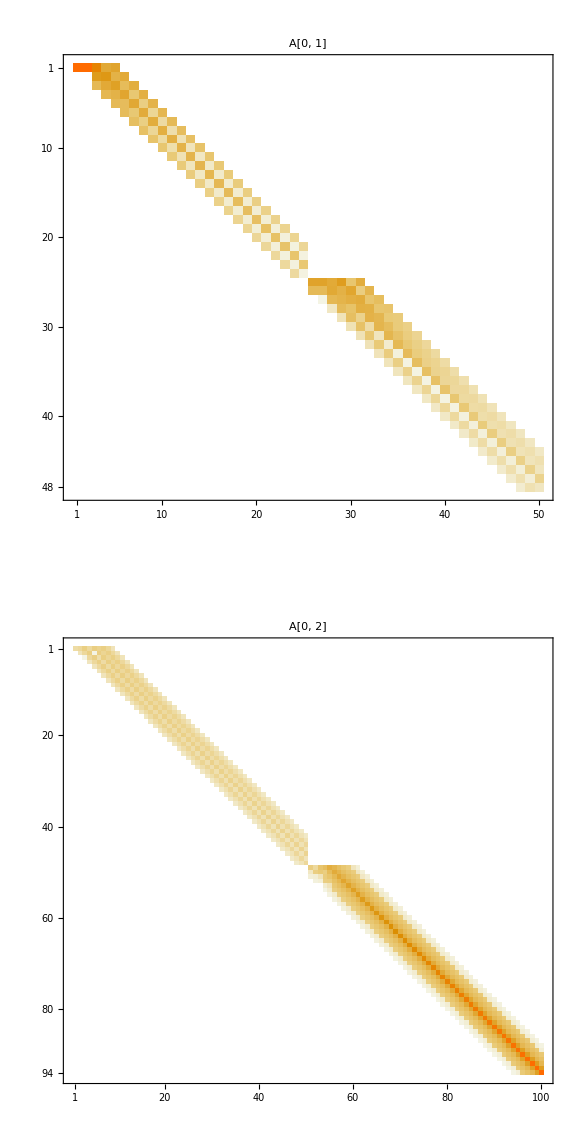

```mathematica
(* get large discretised system without boundary conditions *)
ClearAll[Sprouts`Abulk]
Table[
Sprouts`Abulk[λ,layer]=
Plus@@Table[
	Join@@
Table[(*! always give list of even indices first in option UseParity*)
If[Sprouts`zeroInDomain&&SameQ[layer,1],
SetOptions[MakeMatD,UseParity->{True,First@Sprouts`eid,First@Sprouts`oid}],
SetOptions[MakeMatD,UseParity->{False}]
];
MakeMatD[(Sprouts`drdu[layer])^-j Sprouts`coefeqλ[layer,i,j,λ][Sprouts`rfu[layer][u]],u,j,Sprouts`𝒪d[[layer,i]],Sprouts`n[[layer]]]
		,{i,1,Length[Sprouts`eq⟦layer⟧]}]
	,{j,0,Sprouts`ndiff}]
,{λ,0,Sprouts`λmax},{layer,1,Sprouts`nlayers}];
WriteString["stdout","Bulk Matrices","\n"];
GraphicsGrid[Table[Table[MatrixPlot[Abs@Sprouts`Abulk[λ,layer],PlotLabel->ToString[A[λ,layer]]],{λ,0,Sprouts`λmax}],{layer,1,Sprouts`nlayers}],ImageSize->Large]
```

Right bc matrices

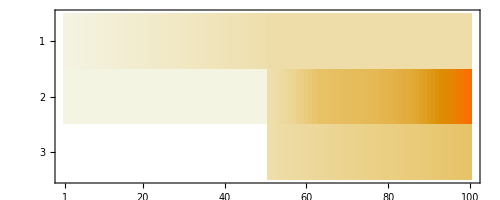

```mathematica
ClearAll[Sprouts`Arbc,Sprouts`Albc]
Table[
Sprouts`Arbc[l]=
Plus@@Table[
	Join@@
Table[(*! always give list of even indices first in option UseParity*)
If[Sprouts`zeroInDomain&&SameQ[Sprouts`nlayers,1],
SetOptions[MakeMatbc,UseParity->{True,First@Sprouts`eid,First@Sprouts`oid}],
SetOptions[MakeMatbc,UseParity->{False}]
];
		MakeMatbc[(Sprouts`drdu[Sprouts`nlayers])^-j Sprouts`coefrbcλ[i,j,l][Sprouts`rfu[Sprouts`nlayers][1]],j,Sprouts`n[[Sprouts`nlayers]],Side->"right"]
		,{i,1,Length[Sprouts`rbc]}]
	,{j,0,Sprouts`ndiff}]
,{l,0,Sprouts`λmax}];
WriteString["stdout","Right bc matrices","\n"];
(MatrixPlot[Abs[#]])&/@Table[Sprouts`Arbc[l],{l,0,Sprouts`λmax}]
(* compute left bc only if 0 is not in the domain *)
If[!Sprouts`zeroInDomain,
SetOptions[MakeMatbc,UseParity->{False}];
Table[
Sprouts`Albc[l]=
Plus@@Table[
		Join@@Table[(*! always give list of even indices first in option UseParity*)
				MakeMatbc[(Sprouts`drdu[1])^-j Sprouts`coeflbcλ[i,j,l][Sprouts`rfu[1][-1]],j,Sprouts`n[[1]],Side->"left"]
			,{i,1,Length[Sprouts`lbc]}]
		,{j,0,Sprouts`ndiff}]
	,{l,0,Sprouts`λmax}];
WriteString["stdout","Left bc matrices","\n"];
(MatrixPlot[Abs[#]])&/@Table[Sprouts`Albc[l],{l,0,Sprouts`λmax}]
];
```

Junction conditions matrices

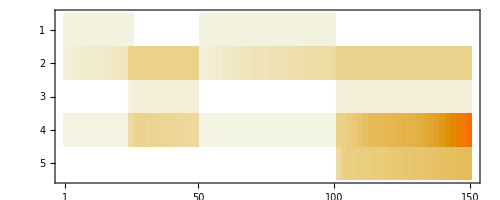
(-Graphics-)

```mathematica
(* get large row matrices of junction conditions *)
ClearAll[Sprouts`Ajc]
Table[
Table[
Sprouts`Ajc[λ,layer]=
Plus@@Table[
		Join@@
	Table[(*! always give list of even indices first in option UseParity*)
	If[Sprouts`zeroInDomain&&SameQ[layer,1],
	SetOptions[MakeMatbc,UseParity->{True,First@Sprouts`eid,First@Sprouts`oid}],
	SetOptions[MakeMatbc,UseParity->{False}]
	];
	Block[{block1,block2},
	block1=MakeMatbc[(Sprouts`drdu[layer])^-j Sprouts`coefjcλ[layer,i,j,λ,"left"][Sprouts`rfu[layer][1(*Last@Sprouts`layer[layer]*)]],j,Sprouts`n[[layer]],Side->"right"];
	SetOptions[MakeMatbc,UseParity->{False}];
	block2=MakeMatbc[(Sprouts`drdu[layer+1])^-j Sprouts`coefjcλ[layer,i,j,λ,"right"][Sprouts`rfu[layer+1][-1(*First@Sprouts`layer[layer+1]*)]],j,Sprouts`n[[layer+1]],Side->"left"];
	Join[block1,block2,2]
	]
			,{i,1,Length[Sprouts`jc⟦layer⟧]}]
		,{j,0,Sprouts`ndiff}]
,{layer,1,Sprouts`nlayers-1}]
,{λ,0,Sprouts`λmax}];
WriteString["stdout","Junction conditions matrices","\n"];
Table[MatrixPlot[Abs[#]]&/@Table[Sprouts`Ajc[λ,layer],{λ,0,Sprouts`λmax}],{layer,1,Sprouts`nlayers-1}]//MatrixForm
```

### Padding

```mathematica
(* pad block matrices to final number of columns *)
ClearAll[Sprouts`AbulkPadded]
Table[
Sprouts`AbulkPadded[λ,k]=(*Sprouts`Abulk[λ,k]*)
Block[{pos},
pos=Total@Table[Dimensions[Sprouts`Abulk[0,kk]]⟦2⟧,{kk,1,k-1}];
SparseArray[Band[{0,pos}+1]->Sprouts`Abulk[λ,k],{Length[Sprouts`Abulk[λ,k]],Sprouts`nColTotal}]
]
,{k,1,Sprouts`nlayers},{λ,0,Sprouts`λmax}];
Table[MatrixPlot/@Table[Sprouts`AbulkPadded[λ,layer],{λ,0,Sprouts`λmax}],{layer,1,Sprouts`nlayers}]//MatrixForm;
```

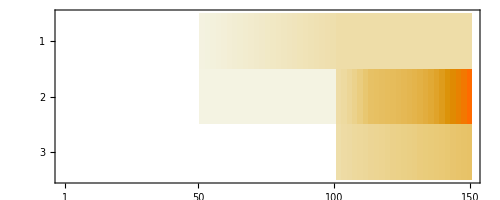

```mathematica
ClearAll[Sprouts`ArbcPadded,Sprouts`AlbcPadded]
Table[
Sprouts`ArbcPadded[λ]=(*Sprouts`Arbc[λ]*)
Block[{pos},
pos=Total@Table[Dimensions[Sprouts`Abulk[0,k]]⟦2⟧,{k,1,Sprouts`nlayers-1}];
SparseArray[Band[{0,pos}+1]->Sprouts`Arbc[λ],{Length[Sprouts`Arbc[λ]],Sprouts`nColTotal}]
]
,{λ,0,Sprouts`λmax}];
MatrixPlot/@Table[Abs@Sprouts`ArbcPadded[l],{l,0,Sprouts`λmax}]
If[!Sprouts`zeroInDomain,
Table[
Sprouts`AlbcPadded[λ]=Sprouts`Albc[λ]
(*SparseArray[Band[{1,1}]->Sprouts`Albc[λ],{Length[Sprouts`Albc[λ]],Sprouts`nColTotal}]*)
,{λ,0,Sprouts`λmax}];
MatrixPlot/@Table[Abs@Sprouts`AlbcPadded[l],{l,0,Sprouts`λmax}]
];
```

```mathematica
Table[
Sprouts`AjcPadded[λ,k]=(*Sprouts`Ajc[λ,k]*)
Block[{pos},
pos=Total@Table[Dimensions[Sprouts`Abulk[0,kk]]⟦2⟧,{kk,1,k-1}];SparseArray[Band[{0,pos}+1]->Sprouts`Ajc[λ,k],{Length[Sprouts`Ajc[λ,k]],Sprouts`nColTotal}]
]
,{k,1,Sprouts`nlayers-1},{λ,0,Sprouts`λmax}];
Table[MatrixPlot/@Table[Sprouts`AjcPadded[λ,layer],{λ,0,Sprouts`λmax}],{layer,1,Sprouts`nlayers-1}]//MatrixForm;
```

### Assemble the final matrices (alternative functions)

```mathematica
(*Table[
Sprouts`Amat[λ]=
ArrayFlatten[{{Sprouts`AlbcPadded[λ]},{Sprouts`AbulkPadded[λ,1]},{Sprouts`ArbcPadded[λ]}}]
,{λ,0,Sprouts`λmax}];
GraphicsGrid[{Table[MatrixPlot[Sprouts`Amat[λ],PlotLabel->"A["<>ToString[λ]<>"]"],{λ,0,Sprouts`λmax}]},ImageSize->Large]*)
```

```mathematica
(*ClearAll[Sprouts`Amat]
Table[
Sprouts`Amat[λ]=
Block[{listofmat,listofind},
If[SameQ[Sprouts`nlayers,1],
listofmat={Sprouts`AbulkPadded[λ,1]}~Join~{Sprouts`ArbcPadded[λ]};,
listofmat=Riffle[Table[Sprouts`AbulkPadded[λ,layer],{layer,1,Sprouts`nlayers}],Table[Sprouts`AjcPadded[λ,layer],{layer,1,Sprouts`nlayers-1}]]~Join~{Sprouts`ArbcPadded[λ]}
];
If[!Sprouts`zeroInDomain,
listofmat={Sprouts`AlbcPadded[λ]}~Join~listofmat
];
listofind=Accumulate[Length/@({0}~Join~Most[listofmat])]+1;
SparseArray[Table[Band[{listofind⟦i⟧,1}]->listofmat⟦i⟧,{i,1,Length[listofind]}]]
]
,{λ,0,Sprouts`λmax}];
GraphicsGrid[{Table[MatrixPlot[Abs@Sprouts`Amat[λ],PlotLabel->"A["<>ToString[λ]<>"]"],{λ,0,Sprouts`λmax}]},ImageSize->Large]*)
```

### Assemble the final matrices

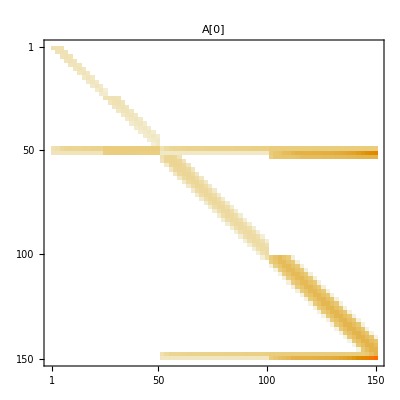

```mathematica
Table[
Sprouts`Amat[λ]=
If[Sprouts`zeroInDomain,
(Join@@Riffle[Table[Sprouts`AbulkPadded[λ,layer],{layer,1,Sprouts`nlayers}],Table[Sprouts`AjcPadded[λ,layer],{layer,1,Sprouts`nlayers-1}]])~Join~(Sprouts`ArbcPadded[λ]),
(Sprouts`AlbcPadded[λ])~Join~(Join@@Riffle[Table[Sprouts`AbulkPadded[λ,layer],{layer,1,Sprouts`nlayers}],Table[Sprouts`AjcPadded[λ,layer],{layer,1,Sprouts`nlayers-1}]])~Join~(Sprouts`ArbcPadded[λ])
]
,{λ,0,Sprouts`λmax}];
GraphicsGrid[{Table[MatrixPlot[Abs@(*Normal@*)Sprouts`Amat[λ],PlotLabel->"A["<>ToString[λ]<>"]"],{λ,0,Sprouts`λmax}]},ImageSize->Large]
```

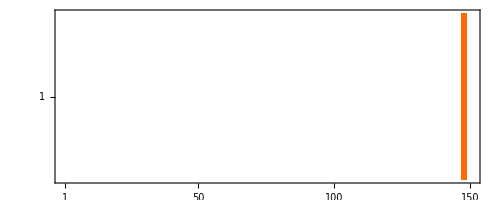

```mathematica
(* assemble bulk of rhs array b if problem of type Ax=b *)
If[!Sprouts`evp,
Table[
If[Sprouts`zeroInDomain&&SameQ[layer,1],
	SetOptions[MakeVec,UseParity->{True,Sprouts`eid,Sprouts`oid}],
	SetOptions[MakeVec,UseParity->{False}]
	];
		Sprouts`bbulk[layer]=SparseArray[Join@@Table[
MakeVec[Sprouts`rhseq[layer,i][][Sprouts`rfu[layer][u]],u,Sprouts`𝒪d⟦layer,i⟧,Sprouts`n[[layer]]]
,{i,1,Length[Sprouts`eq⟦layer⟧]}]];
,{layer,1,Sprouts`nlayers}];
Sprouts`brbc=Join@@Table[First[Sprouts`rhsrbc[i][][Sprouts`rfu[Sprouts`nlayers][1(*Last@Sprouts`layer[Sprouts`nlayers]*)]]],{i,1,Length[Sprouts`rbc]}];
If[!Sprouts`zeroInDomain,
Sprouts`blbc=Join@@Table[First[Sprouts`rhslbc[i][][Sprouts`rfu[1][-1(*First@Sprouts`layer[1]*)]]],{i,1,Length[Sprouts`lbc]}];
];
If[!SameQ[Sprouts`nlayers,1],
Table[
Sprouts`bjc[layer]=Join@@Table[SparseArray@First[(Normal[Sprouts`rhsjc[layer,i,"left"][][r]]/.((#->0)&/@Flatten@Sprouts`listvar))/.r->Sprouts`rfu[layer][1(*Last@Sprouts`layer[layer]*)]],{i,1,Length[Sprouts`jc⟦layer⟧]}]
,{layer,1,Sprouts`nlayers-1}]
];
Sprouts`bvec=
-SparseArray@If[Sprouts`zeroInDomain,
(Join@Flatten@Riffle[Table[Sprouts`bbulk[layer],{layer,1,Sprouts`nlayers}],Table[Sprouts`bjc[layer],{layer,1,Sprouts`nlayers-1}]])~Join~(Sprouts`brbc),
(Sprouts`blbc)~Join~(Join@Flatten@Riffle[Table[Sprouts`bbulk[layer],{layer,1,Sprouts`nlayers}],Table[Sprouts`bjc[layer],{layer,1,Sprouts`nlayers-1}]])~Join~(Sprouts`brbc)
];
MatrixPlot@Abs@{Sprouts`bvec}
]
```

```mathematica
sol=LinearSolve[Sprouts`Amat[0],Sprouts`bvec]//Chop
```

{0.58434,0.58434,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2.59505×10^-8,-2.59505×10^-8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.29711,0.141062,0.0120247,-0.000564232,0.0000420085,-2.91985×10^-6,1.93311×10^-7,-1.23423×10^-8,7.66171×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-5.60896×10^-8,-3.67069×10^-9,5.0453×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Flatten@MapThread[ConstantArray,{MapAt[#/2&,Sprouts`n,1],Length/@Sprouts`scalars}]
sol=TakeList[sol,%]
```

{25,25,50,50}

{{0.58434,0.58434,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-2.59505×10^-8,-2.59505×10^-8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1.29711,0.141062,0.0120247,-0.000564232,0.0000420085,-2.91985×10^-6,1.93311×10^-7,-1.23423×10^-8,7.66171×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-5.60896×10^-8,-3.67069×10^-9,5.0453×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
Sprouts`scalars
```

{{δϕ1,pol1},{δϕ2,pol2}}

```mathematica
Total[sol[[3]]]-1
```

0.44967

```mathematica
-6 Total[sol[[4]]]G/.parameters
```

0.789581

```mathematica
(*Table[Export["./A"<>ToString[λ]<>".mtx",Sprouts`Amat[λ]/Norm[Sprouts`Amat[0],"Frobenius"]],{λ,0,Sprouts`λmax}]*)
```

```mathematica
(*Export["~/tmp/m.mat",{"A"->Sprouts`Amat[0],"B"->Sprouts`Amat[1]},"LabeledData"]*)
```

```mathematica
(*{eig,eigv}=Eigensystem[{Sprouts`Amat[0],-Sprouts`Amat[2]}];
filteredIndices=Flatten[Position[eig,_?(Im[#]==0&&#!=ComplexInfinity&)]];
feig=eig[[filteredIndices]];
feigv=eigv[[filteredIndices]];
√feig*)
```

```mathematica
<<"~/ownCloud/Shared/spectral.m"
```

```mathematica
-(Total@sol[[4]]+Total@DCheb[sol[[4]]])G/.parameters
```

0.135267

```mathematica
-Total@DCheb[TimesCheb[{0,1},sol[[4]]]]G/.parameters
```

0.135267